```mathematica
(* With s-orbitals *)
```

```mathematica
(* *)
A=9.52; (* in Anstrom*)
(*A1=A {0,1,1}/2;A2=A{1,0,1}/2;A3=A{1,1,0}/2;
these do not match with the FCC Bravais vectors used to calculate reciprocal lattices
- turns out this change doesn't make any difference*)
 A1=A {1,1,0}/4;A2=A{1,0,1}/4;A3=A{0,1,1}/4;

(*Nearest neighbour distance*)
dnn= A/(2 Sqrt[2]);
(*Vss for nearest neighbour by Liu-Allen 1/d^2 fitting, Vss from just table 2*)
 12.5/(3.36583)^2;
Vsp= 1.10338;
Vss = -0.608;

FCCBravaisVectors=A {{1/4,1/4,0},{1/4,0,1/4},{0,1/4,1/4}};FCCReciprocalVectors={(2 π Cross[FCCBravaisVectors[[2]],FCCBravaisVectors[[3]]])/(FCCBravaisVectors[[3]].Cross[FCCBravaisVectors[[1]],FCCBravaisVectors[[2]]]),(2 π Cross[FCCBravaisVectors[[3]],FCCBravaisVectors[[1]]])/(FCCBravaisVectors[[3]].Cross[FCCBravaisVectors[[1]],FCCBravaisVectors[[2]]]),(2 π Cross[FCCBravaisVectors[[1]],FCCBravaisVectors[[2]]])/(FCCBravaisVectors[[3]].Cross[FCCBravaisVectors[[1]],FCCBravaisVectors[[2]]])};
G1=FCCReciprocalVectors[[1]];
G2=FCCReciprocalVectors[[2]];
G3=FCCReciprocalVectors[[3]];
```

```mathematica
(* high symmetry momenta *)
ΓΓ={0,0,0};XX=(G1+G3)/2;WW=(3 G1+G2+2 G3)/4;LL=(G1+G2+G3)/2;
path[t_]:=UnitStep[t] UnitStep[Norm[XX]-t]t XX/Norm[XX]+UnitStep[t-Norm[XX]] UnitStep[Norm[XX]+Norm[WW-XX]-t]((Norm[XX]+Norm[WW-XX]-t)/Norm[WW-XX] XX+(t-Norm[XX])/Norm[WW-XX] WW)+UnitStep[t-Norm[XX]-Norm[WW-XX]] UnitStep[Norm[XX]+Norm[WW-XX]+Norm[WW-LL]-t]((Norm[XX]+Norm[WW-LL]+Norm[WW-XX]-t)/Norm[WW-LL] WW+(t-Norm[XX]-Norm[WW-XX])/Norm[WW-LL] LL)+UnitStep[t-Norm[XX]-Norm[WW-XX]-Norm[WW-LL]] UnitStep[Norm[XX]+Norm[WW-XX]+Norm[WW-LL]+Norm[LL]-t]((Norm[XX]+Norm[WW-LL]+Norm[WW-XX]+Norm[LL]-t)/Norm[LL] LL);
```

```mathematica
n12={0,1,1}/√2;n13={1,0,1}/√2;n14={1,1,0}/√2;n23={1,-1,0}/√2;n24={1,0,-1}/√2;n34={0,1,-1}/√2;
DO[n_]:={n,Normalize[Cross[n,{1,0,0}]],Normalize[Cross[n,Cross[n,{1,0,0}]]]};
DO12=DO[n12];
DO13=DO[n13];DO14=DO[n14];DO23=DO[n23];DO24=DO[n24];DO34=DO[n34];
```

```mathematica
(* fitting from Liu Allen Bi model; p orbitals; 1/d^2 rule *)
{Vppσ1,Vσ2,Vσ3}={1.5668031918649818,0.5222677306216607,0.39170079796624546};
{Vppπ1,Vπ2,Vπ3}=-{0.4325259515570936,0.14417531718569787,0.1081314878892734};
```

```mathematica
Vd1={{Vppσ1,0,0},{0,Vppπ1,0},{0,0,Vppπ1}};
V1d12=Transpose[DO12].Vd1.DO12;
V1d13=Transpose[DO13].Vd1.DO13;
V1d14=Transpose[DO14].Vd1.DO14;V1d23=Transpose[DO23].Vd1.DO23;V1d24=Transpose[DO24].Vd1.DO24;V1d34=Transpose[DO34].Vd1.DO34;
```

```mathematica
(*To introduce coupling between s orbitals, I add another row and column making the orbital coupling matrix to be 4x4 instead of 3x3. The 1-1th entry of the matrix will be Vss *)
c={0,0,0};
r={Vss,0,0,0};
V1d12s = Join[{r},Transpose[Join[{c},Transpose[V1d12]]]];
V1d13s = Join[{r},Transpose[Join[{c},Transpose[V1d13]]]];
V1d14s = Join[{r},Transpose[Join[{c},Transpose[V1d14]]]];
V1d23s = Join[{r},Transpose[Join[{c},Transpose[V1d23]]]];
V1d24s = Join[{r},Transpose[Join[{c},Transpose[V1d24]]]];
V1d34s = Join[{r},Transpose[Join[{c},Transpose[V1d34]]]];
```

```mathematica
(* spin-orbit *)
(*No s-s spin orbit coupling so I just make all these 4x4 with 1st row and 1st column of zeros*)
λSO=1.5;
Hλxyup={{0,0,0,0},{0,0,-I λSO/3,0},{0,I λSO/3,0,0},{0,0,0,0}};Hλxydown=-Hλxyup;Hλdownup={{0,0,0,0},{0,0,0,-λSO/3},{0,0,0,-I λSO/3},{0,λSO/3,I λSO/3,0}}; (* changed sign in front of real lambda here*) Hλupdown=Transpose[Conjugate[Hλdownup]];
```

```mathematica
(* Using Liu Allen fitting *)
(*Now each of these H are a 4x4 matrices*)
HLA12[k_]:=(1+Exp[-I k.A1])V1d12s
HLA13[k_]:=(1+Exp[-I k.A2])V1d13s;HLA14[k_]:=(1+Exp[-I k.A3])V1d14s;HLA23[k_]:=(1+Exp[I k.(A1-A2)])V1d23s;HLA24[k_]:=(1+Exp[I k.(A1-A3)])V1d24s;HLA34[k_]:=(1+Exp[I k.(A2-A3)])V1d34s;
HLA21[k_]:=(1+Exp[I k.A1])V1d12s;HLA31[k_]:=(1+Exp[I k.A2])V1d13s;HLA41[k_]:=(1+Exp[I k.A3])V1d14s;HLA32[k_]:=(1+Exp[-I k.(A1-A2)])V1d23s;HLA42[k_]:=(1+Exp[-I k.(A1-A3)])V1d24s;HLA43[k_]:=(1+Exp[-I k.(A2-A3)])V1d34s;
HLAnn[k_]:=ArrayFlatten[{{0,HLA12[k],HLA13[k],HLA14[k]},{HLA21[k],0,HLA23[k],HLA24[k]},{HLA31[k],HLA32[k],0,HLA34[k]},{HLA41[k],HLA42[k],HLA43[k],0}}]; 
MatrixForm[HLAnn[k_]];

(* with Liu Allen spin orbit *)
HLAnnup[k_]:=ArrayFlatten[{{Hλxyup,HLA12[k],HLA13[k],HLA14[k]},{HLA21[k],Hλxyup,HLA23[k],HLA24[k]},{HLA31[k],HLA32[k],Hλxyup,HLA34[k]},{HLA41[k],HLA42[k],HLA43[k],Hλxyup}}];
HLAnndown[k_]:=ArrayFlatten[{{Hλxydown,HLA12[k],HLA13[k],HLA14[k]},{HLA21[k],Hλxydown,HLA23[k],HLA24[k]},{HLA31[k],HLA32[k],Hλxydown,HLA34[k]},{HLA41[k],HLA42[k],HLA43[k],Hλxydown}}];
HLAupdown=ArrayFlatten[{{Hλupdown,0,0,0},{0,Hλupdown,0,0},{0,0,Hλupdown,0},{0,0,0,Hλupdown}}];HLAdownup=Transpose[Conjugate[HLAupdown]];
HtotLA[k_]:=ArrayFlatten[{{HLAnnup[k],HLAupdown},{HLAdownup,HLAnndown[k]}}];
```

```mathematica
Ef=-0.1872246741793219;
```

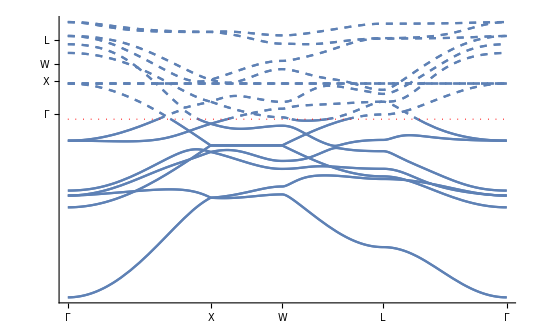

```mathematica
(* Liu Allen fitting with spin orbit *)
pvaltotLA=Plot[Sort[Eigenvalues[HtotLA[path[t]]]],{t,0,Norm[XX]+Norm[WW-LL]+Norm[WW-XX]+Norm[LL]},Ticks->{{{0,Γ},{Norm[XX],X},{Norm[XX]+Norm[WW-XX],W},{Norm[XX]+Norm[WW-LL]+Norm[WW-XX],L},{Norm[XX]+Norm[WW-LL]+Norm[WW-XX]+Norm[LL],Γ}}},PlotRange->{-8,Ef}];
pcontotLA=Plot[Sort[Eigenvalues[HtotLA[path[t]]]],{t,0,Norm[XX]+Norm[WW-LL]+Norm[WW-XX]+Norm[LL]},PlotStyle->Dashed,PlotRange->{Ef,5}];
fl=Plot[Ef,{t,0,Norm[XX]+Norm[WW-LL]+Norm[WW-XX]+Norm[LL]},PlotStyle->Directive[Red,Thin,Dotted]];
Show[pvaltotLA,pcontotLA,fl,PlotRange->All]
```

```mathematica
(* Fermi energy *)
LLk=10;
mesheng=Sort[Flatten[Table[Eigenvalues[HtotLA[m1/LLk G1+m2/LLk G2+m3/LLk G3]],{m1,-LLk/2+1,LLk/2},{m2,-LLk/2+1,LLk/2},{m3,-LLk/2+1,LLk/2}]],#1<#2&];
Ef=mesheng[[14 LLk^3]]
Length[mesheng]==32 LLk^3
```

-0.187225

True